# PRACTICAL 1 : Solution of First Order Differential Equation

## ODEs in which there is a single independent variable and one or more dependent variable.

DSolve[eqn, y[x], x] : solving a differential equation for y[x]
DSolve[{eqn1, eqn2, ......}, {y1[x], y2[x],.....}, x] :
Solving a system of differential equation for yi[x]

Ques 1 : Solve dy/dx=y

```mathematica
x=2
```

2

```mathematica
y=2
```

2

```mathematica
x+y
```

4

```mathematica
x=.
```

```mathematica
y=.
```

```mathematica
z=.
```

```mathematica
sol1=DSolve[{ y'[x] == y[x] }, y[x], x]
```

{{y[x]→ⅇ^x C[1]}}

```mathematica
A=y[x]/.sol1/.{C[1]-> 1}
```

{ⅇ^x}

```mathematica
y[x]
```

y[x]

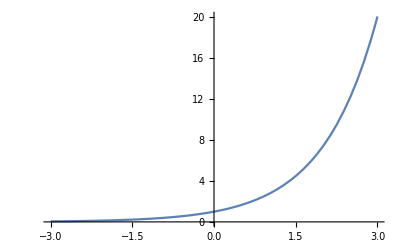

```mathematica
Plot[{A} , {x,-3,3}]
```

You can pick out a specific solution by using /. (Replace All)

## Straight Integration

```mathematica
x=.
```

```mathematica
y=.
```

```mathematica
Clear All
```

All Clear

### This equation is solved by simply integrating the right hand side with respect to x:

```mathematica
sol22=DSolve[y'[x] == x^2, y[x], x]
```

{{y[x]→x^3/3+C[1]}}

```mathematica
B1=y[x]/.sol22/.{C[1]->2}
```

{2+x^3/3}

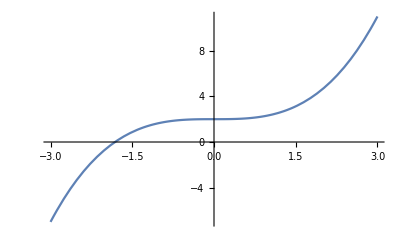

```mathematica
Plot[B1, {x,-3,3}]
```

### ANOTHER METHOD :

```mathematica
B1=Table[y[x]/.sol22/.{C[1]->k},{k,2,5}]
```

{{2+x^3/3},{3+x^3/3},{4+x^3/3},{5+x^3/3}}

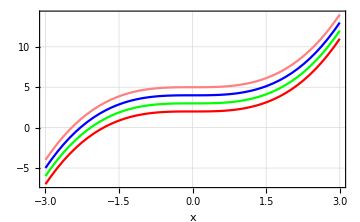

```mathematica
Plot[B1, {x,-3,3}, PlotStyle-> {Red, Green, Blue , Pink}, GridLines -> Automatic, Frame -> True, AxesOrigin->{0,0}, AxesLabel->Automatic, ImageSize->Medium]
```

### Separable Equations

### The general solution to this equation is found by separation of variable:

```mathematica
A=DSolve[y'[x]== 2*x*y[x]/(x+1), y[x], x]
```

{{y[x]→ⅇ^(2 (x-Log[1+x])) C[1]}}

```mathematica
B1=Table[y[x]/.A/.{C[1]->k}, {k,2,5}]
```

{{2 ⅇ^(2 (x-Log[1+x]))},{3 ⅇ^(2 (x-Log[1+x]))},{4 ⅇ^(2 (x-Log[1+x]))},{5 ⅇ^(2 (x-Log[1+x]))}}

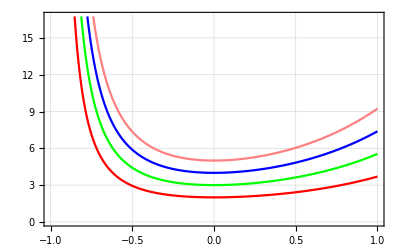

```mathematica
Plot[{B1}, {x,-1,1}, PlotStyle->{Red, Green, Blue, Pink}, GridLines-> Automatic, Frame->True, AxesOrigin->{0,0}]
```

### Initial value problem

### The solution of this type differential equations does not contain constant

```mathematica
sol2=DSolve[{y'[x] == y[x]+2/x * y[x], y[1]==1}, y[x], x]
```

{{y[x]→ⅇ^(-1+x) x^2}}

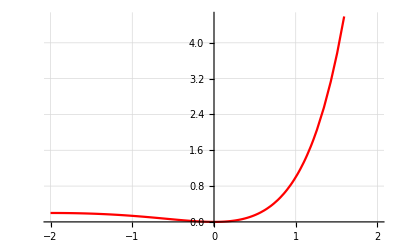

```mathematica
Plot[y[x]/.sol2, {x,-2,2}, PlotStyle->{Red}, GridLines-> Automatic]
```

### Homogenous Equations

### here is a homogenous equation in which the total degree of both the numerator and the denominator of the righthand side is name. The two parts of the solution list give branches of the integral curves in the form :

```mathematica
sol3=DSolve[y'[x]== (x+y[x])/(x), y[x], x]
```

{{y[x]→x C[1]+x Log[x]}}

```mathematica
sol4=Table[y[x]/.sol3/.{C[1]-> k}, {k,2,5}]
```

{{2 x+x Log[x]},{3 x+x Log[x]},{4 x+x Log[x]},{5 x+x Log[x]}}

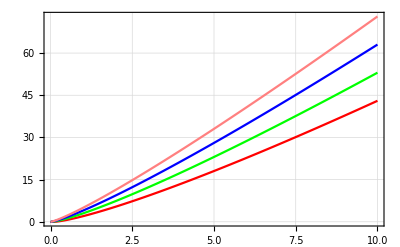

```mathematica
Plot[{sol4},{x,0,10}, PlotStyle->{Red, Green, Blue , Pink}, GridLines->Automatic, Frame->True, AxesOrigin->{0,0}]
```

### Linear First-Order Equations

### The following is a linear first order ODE because both y[x] and its derivative y’[x] occur in it with power 1 and is the highest derivative. Note that the solution contains the imaginary error function Erfi:

```mathematica
sol5=DSolve[y'[x]+y[x]/(x) ==x^2, y[x], x]
```

{{y[x]→x^3/4+C[1]/x}}

```mathematica
sol6=Table[y[x]/. sol5/. {C[1]->k}, {k,2,5}]
```

{{2/x+x^3/4},{3/x+x^3/4},{4/x+x^3/4},{5/x+x^3/4}}

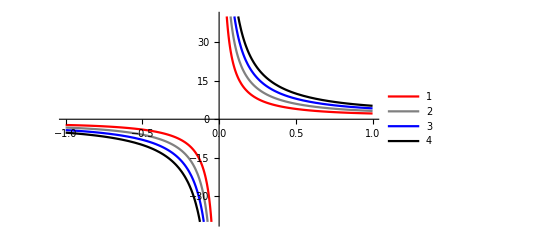

```mathematica
Plot[{sol6}, {x,-1,1}, PlotStyle->{Red, Gray, Blue, Black}, PlotLegends -> Automatic]
```

```mathematica
Plot[{sol6}, {x,-1,1}, PlotStyle->{Red, Gray, Blue, Black}, PlotLegends->Placed[Automatic, Below]]
```

-Graphics-

```mathematica
sol7=DSolve[{y'[x]*Tan[x]==2*y[x]-8, y[Pi/2]==0}, y[x], x]
```

{{y[x]→-4 (-1+Sin[x]^2)}}

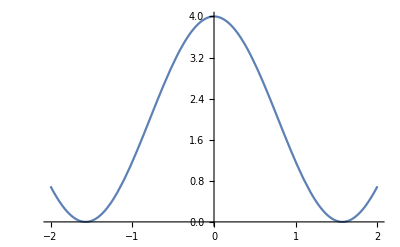

```mathematica
Plot[y[x]/.sol7, {x,-2,2}]
```

### Bernoulli Equations

### A Bernoulli Equation is a first - order equation of the form y’(x) + P(x) y(x) = Q(x) y (x)^n

```mathematica
sol8=DSolve[x*y'[x] + y[x]== y[x]^2x^2+1, y[x], x]
```

{{y[x]→Tan[x+C[1]]/x}}

```mathematica
sol9=Table[y[x]/.sol8/.{C[1]->k}, {k,1,4}]
```

{{Tan[1+x]/x},{Tan[2+x]/x},{Tan[3+x]/x},{Tan[4+x]/x}}

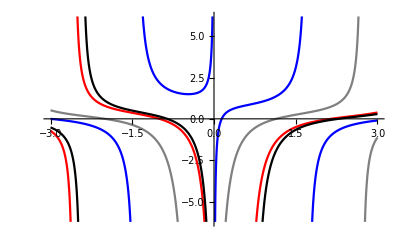

```mathematica
Plot[{sol9}, {x,-3,3}, PlotStyle->{Red, Gray, Blue, Black}, PlotLegends->Placed["Ëxpressions", Right]]
```

### Exact Equations

Let M(x,y) and N(x,y) be two smooth functions having continuous partial derivatives in some domain R^2 without holes. A differential equation, written in differentials :
					M(x,y) dx + N(x,y)dy = 0
is called Exact if and only if 
					dM(x,y)/dy = dN(x,y)/dz
or there exists a smooth function v(x,y) called the potential function such that its total differential :
					dv=M(x,y) dx + N(x,y) =0

### Classify the differential equation as exact or not

```mathematica
D[f(x,y), differentiatewithrespectto]
D[f(x,y), x]diffwrtx
```

```mathematica
M1[x_, y_] := (x*y^2+x)
```

```mathematica
N1[x_, y_] := (y*x^2)
```

```mathematica
Simplify[D[M1[x,y],y] - D[N1[x,y],x]]
```

0

```mathematica
eqn=y'[x] == -M1[x,y[x]]/N1[x,y[x]]
```

y'[x]==(-x-x y[x]^2)/(x^2 y[x])

```mathematica
sol11=DSolve[eqn, y[x],x]
```

```mathematica
{{y[x]->-(√(ⅇ^(2 C[1])-x^2))/x},{y[x]->(√(ⅇ^(2 C[1])-x^2))/x}}
```

{{y[x]→-(√(ⅇ^(2 C[1])-x^2))/x},{y[x]→(√(ⅇ^(2 C[1])-x^2))/x}}

```mathematica
p[x_, y_] := -(5x^2 - 2y^2+11)
```

```mathematica
q[x_,y_] := (Sin[y]+4xy+3)
```

```mathematica
Simplify[D[p[x,y],y]-D[q[x,y],x]]
```

4 y